# UpSetChart

#### Restart Kernel

```mathematica
Quit[]
```

#### Import UpSetChart

```mathematica
$Path=Prepend[$Path,NotebookDirectory[]];
<<UpSetChart`
```

#### Demonstration Data

```mathematica
$UpSetDemoData1
```

<|a→{7,77,53,95,42,41},b→{51,88,87,67,90,37,96},c→{15,87,99,6,20,87,98,68},d→{46,85,6,90},e→{72,97,15,55,87}|>

#### UpSet with various options

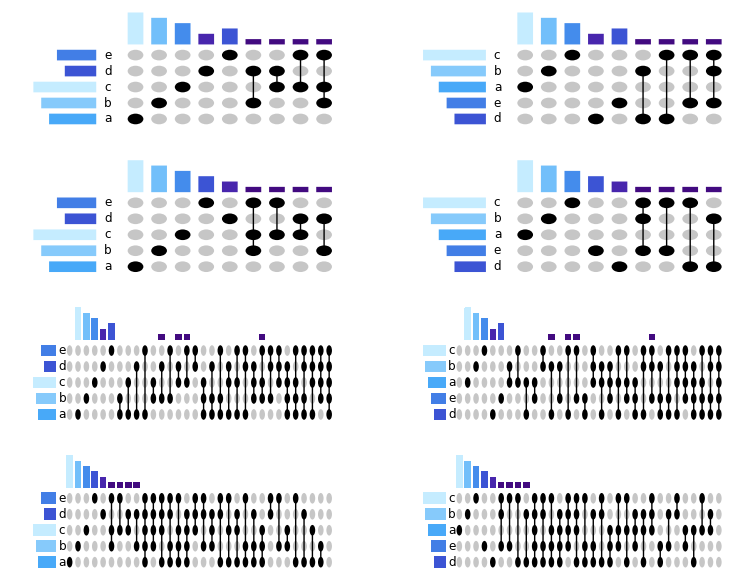

```mathematica
GraphicsGrid[
Partition[Flatten[
Table[
UpSetChart[$UpSetDemoData1, "DropEmpty"->de ,"IntersectionSortBy"->iSB, "SetSortBy"->sSB,"Verbose"->False],
{de,{True, False}},{iSB,{"Name","Cardinality"}},{sSB,{"Name","Cardinality"}}]
],{2}]]
```

```mathematica
Options["a"->b,"GridOptions"->Automatic];

func[OptionsPattern[]]:=Module[{grid},
grid=OptionValue["GridOptions"];
```

#### Demo Data 2

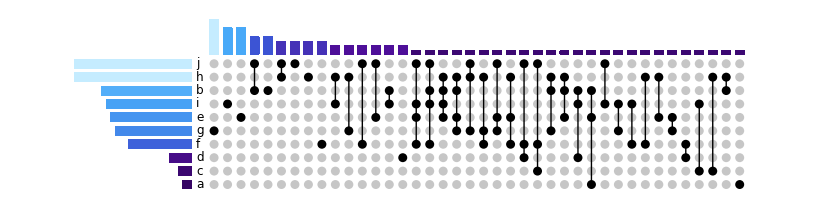

```mathematica
UpSetChart[$UpSetDemoData2, "DropEmpty"->True ,"IntersectionSortBy"->"Cardinality", "SetSortBy"->"Cardinality","Verbose"->False]
```

#### Random Data

Dropping empty sets

Calculating elements unique to intersections

Hang tight! This requires 32768 comparisons.

Dropping empty comparisons

Sorting sets by Cardinality

Sorting comparisons by Cardinality

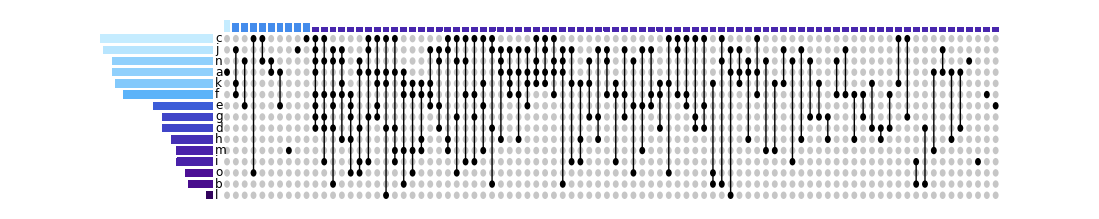

```mathematica
sets=UpSetDummyData[15, 40];UpSetChart[sets, "DropEmpty"->True ,"IntersectionSortBy"->"Cardinality", "SetSortBy"->"Cardinality","Verbose"->True]
```

```mathematica
?UpSetChart
```

UpSetChart[Association[setName->List[element1, element2,..., elementN]],...].

```mathematica
StringJoin
```